Statistical Metric | Value
Target Depth (m) | 10
Total Leaf Nodes Generated | 24576
Distinct Values Found | 5
Statistical Mode(s) | {131072}
Expected Value (Mean) | 165888.

Exact Frequency Distribution:

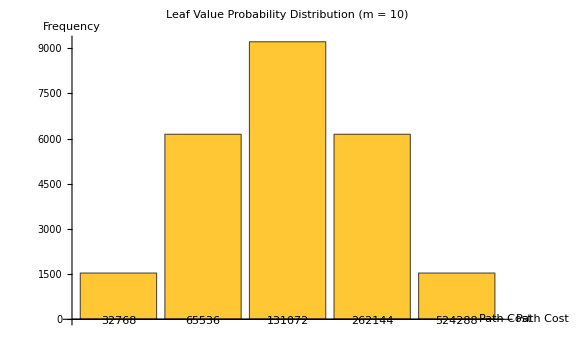

```mathematica
Evaluate8PuzzleStats[m_Integer:4]:=Module[{neighbors,multiplier,initialState,finalStates,finalValues,totalLeaves,mode,mean},(*1. Define the 3x3 grid graph layout for the blank tile positions (1 to 9)*)neighbors=<|1->{2,4},2->{1,3,5},3->{2,6},4->{1,5,7},5->{2,4,6,8},6->{3,5,9},7->{4,8},8->{5,7,9},9->{6,8}|>;
(*2. Define path multipliers based on the branching rules*)multiplier[pos_]:=Which[MemberQ[{1,3,7,9},pos],2,(*Corners:2 moves->multiply by 2*)MemberQ[{2,4,6,8},pos],4,(*Edges:3 moves->multiply by 4*)pos==5,4                     (*Center:4 moves->multiply by 4*)];
(*3. Initial State:position 3 (starting corner),value=1,path count=1*)initialState=<|{3,1}->1|>;
(*4. Propagate the state layer-by-layer up to depth m using state aggregation*)finalStates=Nest[Function[states,Merge[Flatten[KeyValueMap[Function[{key,count},With[{pos=key[[1]],val=key[[2]]},Table[{n,val*multiplier[pos]}->count,{n,neighbors[pos]}]]],states]],Total]],initialState,m];
(*5. Collapse grid positions to isolate final values and their exact frequencies*)finalValues=KeySort[Merge[KeyValueMap[#1[[2]]->#2&,finalStates],Total]];
(*6. Calculate Statistical Means*)totalLeaves=Total[finalValues];
mode=Keys[Select[finalValues,#==Max[finalValues]&]];
mean=N[Total[KeyValueMap[#1*#2&,finalValues]]/totalLeaves];
(*7. Format and Print Report*)Print[TextGrid[{{"Statistical Metric","Value"},{"Target Depth (m)",m},{"Total Leaf Nodes Generated",totalLeaves},{"Distinct Values Found",Length[finalValues]},{"Statistical Mode(s)",mode},{"Expected Value (Mean)",mean}},Frame->All,Background->{{LightGray,None},{LightBlue,None}}]];
Print["\nExact Frequency Distribution:"];
Print[Dataset[finalValues]];
(*8. Visual Distribution Graph*)BarChart[finalValues,ChartLabels->Automatic,PlotLabel->"Leaf Value Probability Distribution (m = "<>ToString[m]<>")",AxesLabel->{" Path Cost","Frequency"},ImageSize->Large]]

Evaluate8PuzzleStats[10]
```